(* 1 *)
Nathan Solomon
UID: 905 746 764
nathansolomon1678@gmail.com
HW #1

(* 2 *)
Previous experience:
	I’ve used C++, Python, and a bit of JavaScript before. I’ve taken PIC 10A and PIC 16A, but have also used those languages for other projects and extracurriculars. I am definitely most comfortable with Python.

```mathematica
(* 3 *)
Remove["Global`*"]

a = ((3.9122×10^2)^(1/3) √(2.017×10^-5))/(3.661×10^-4);
a
NumberForm[a, 4]
```

89.7209

89.72

```mathematica
(* 4 *)
Factor[2 x^4 y^6 + 6 x^2 y^3 - 20]
```

2 (-2+x^2 y^3) (5+x^2 y^3)

```mathematica
(* 5 *)
Remove["Global`*"]
(* Using Simplify instead of FullSimplify will only partially simplify it *)
FullSimplify[Sec[θ] Tan[θ] (Sec[θ] + Tan[θ]) + (Sec[θ] - Tan[θ])]
```

Sec[θ]^3+Tan[θ]^3

```mathematica
(* 6 *)
Remove["Global`*"]

a = -1.5×10^-7;
b = 5×10^9;
c = -500;
x[t_] := a t^2 + b t + c;
roots = (-b + {1, -1}*√(b^2 - 4 a c))/(2 a)
(* That equation said the first root is zero! Since 4ac is so small compared to b^2,
the numerator experienced loss of significance. One way to fix that is to notes that
the product of the roots of a quadratic is c*a. Alternatively, you could use Mathematica's
built-in `Solve` or `FindRoots` methods. *)
roots[[1]] = c/(a roots[[2]]);
Print["Actual roots: ", roots, "\n"]


vAvg[t_] := (x[t] - x[0])/t
Print["Average velocity from t=0 to the first root (t=", roots[[1]], "): ", vAvg[roots[[1]]]]
Print["Average velocity from t=0 to the second root (t=", roots[[2]], "): ", vAvg[roots[[2]]]]
(* Mathematica thinks that x[roots[[1]]] and x[roots[[2]]] are not exactly zero, which I assume is because
of rounding errors. But since we know that those are roots, and we only use vAvg on the roots of x,
we can replace x[t] with 0, or just simplify it to vAvg[t]:=-c/t (since x[0]=c) *)
vAvg[t_] := -c/t
Print["\nRepeating those calulations, except correctly now:"]
Print["Average velocity from t=0 to the first root (t=", roots[[1]], "): ", vAvg[roots[[1]]]]
Print["Average velocity from t=0 to the second root (t=", roots[[2]], "): ", vAvg[roots[[2]]]]
```

{0.,3.33333×10^16}

Actual roots: {1.×10^-7,3.33333×10^16}

Average velocity from t=0 to the first root (t=1.×10^-7): 5.×10^9

Average velocity from t=0 to the second root (t=3.33333×10^16): 0.

Repeating those calulations, except correctly now:

Average velocity from t=0 to the first root (t=1.×10^-7): 5.×10^9

Average velocity from t=0 to the second root (t=3.33333×10^16): 1.5×10^-14

```mathematica
(* 7 *)
Remove["Global`*"]

Subscript[σ, 1] = {{0, 1}, {1, 0}};
Subscript[σ, 2] = {{0, -I}, {I, 0}};
Subscript[σ, 3] = {{1, 0}, {0, -1}};

Subscript[σ, 1] . Subscript[σ, 1] == IdentityMatrix[2]
Subscript[σ, 2] . Subscript[σ, 2] == IdentityMatrix[2]
Subscript[σ, 3] . Subscript[σ, 3] == IdentityMatrix[2]
- I Subscript[σ, 1] . Subscript[σ, 2] . Subscript[σ, 3] == IdentityMatrix[2]

Subscript[σ, 1] . Subscript[σ, 2] - Subscript[σ, 2] . Subscript[σ, 1] == 2 I Subscript[σ, 3]

(* Note that squaring a vector or matrix squares it ELEMENT-WISE, like in this example:
	A = {{1, 2}, {3, 4}};
	A^2 == {{1,4},{9,16}}
	MatrixPower[A, 2] == {{7,10},{15,22}}
	A . A == {{7,10},{15,22}}
*)
```

True

True

True

«2 more identical outputs»

Position: (-t Cos[t]+t Cos[π/6+t]+Sin[t]
-Cos[t]-t Sin[t]+t Sin[π/6+t])

Velocity: (Cos[π/6+t]+t Sin[t]-t Sin[π/6+t]
-t Cos[t]+t Cos[π/6+t]+Sin[π/6+t])

Acceleration: (t Cos[t]-t Cos[π/6+t]+Sin[t]-2 Sin[π/6+t]
-Cos[t]+2 Cos[π/6+t]+t Sin[t]-t Sin[π/6+t])

Speed: √(1-t-(-2+√3) t^2)

Angle between acceleration and velocity vectors at time t=3: 1.0626 radians

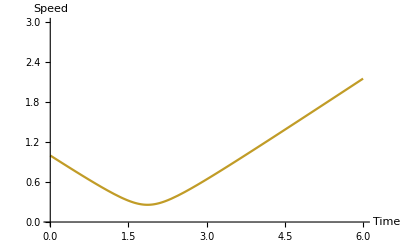

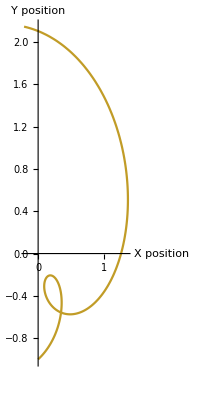

```mathematica
(* 8 *)
Remove["Global`*"]

r[t_] := {
	Sin[t] - t Cos[t] + t Cos[t + Pi / 6],
	t Sin[t + Pi / 6] - t Sin[t] - Cos[t]
}
v[t_] = D[r[t], t];
a[t_] = D[v[t], t];
(* Using Norm[v[t]] will write the speed with |Subscript[v, x]^2| and |Subscript[v, y]^2| instead of just Subscript[v, x]^2 and Subscript[v, y]^2, which is unnecessary because
we're assuming the components of velocity are real numbers. The method below writes the same thing in a less ugly way *)
speed[t_] := Sqrt[(v[t][[1]])^2 + (v[t][[2]])^2]

Print["Position: ", MatrixForm[r[t]]]
Print["Velocity: ", MatrixForm[v[t]]]
Print["Acceleration: ", MatrixForm[a[t]]]
Print["Speed: ", speed[t] // Simplify]

angleBetweenVectors[vec1_, vec2_] := ArcCos[(vec1 . vec2)/(Norm[vec1] Norm[vec2])]
Print["Angle between acceleration and velocity vectors at time t=3: ", N[angleBetweenVectors[v[3], a[3]]], " radians\n"]

Plot[speed[t], {t, 0, 6}, AxesLabel -> {"Time", "Speed"}, PlotRange -> {0, 3}]
ParametricPlot[r[t], {t, 0, 6}, AxesLabel -> {"X position", "Y position"}]
```

Due Tuesday, 24 Jan
Each project will be worth 10 points.  Grades will be based on completeness, accuracy, presentation, and individuality.
Submit by emailing the *.nb file to corbin@physics.ucla.edu with the subject line “[Physics 170E]”